```mathematica
SetDirectory@NotebookDirectory[];
```

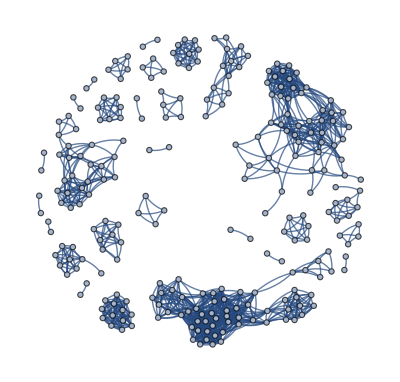

```mathematica
graphD5=Import["../../Data/graphD501.wxf"]
```

```mathematica
colorCommunities[graph_]:=HighlightGraph[graph,Map[Subgraph[graphD5,#]&,FindGraphCommunities[graph]]]
```

```mathematica
DynamicModule[{vertexClicked={},graph=graphD5,edges=EdgeList[graphD5],vertices=Union@@List@@@EdgeList[graphD5],clickable=False},
Panel[
Column[{
Row[{
Spacer[10],
ActionMenu["Communities",{
"Highlight":>(graph=colorCommunities[graph]),
"Export":>Export["communities.wxf",FindGraphCommunities[graph]]
}],
Spacer[10],
ActionMenu["Connected components",{
"Highlight":>(graph=HighlightGraph[graph,ConnectedComponents[graph]]),
"Export":>Export["connectedComponents.wxf",ConnectedComponents[graph]]
}],
Spacer[10],
Button["Select Vertices",clickable=Not[clickable];If[clickable,graph=Annotate[graph,
VertexShapeFunction->(EventHandler[Disk[#1,0.05],
"MouseClicked":>
(vertexClicked=Append[vertexClicked,#2];graph=Annotate[graph,VertexStyle->Thread[vertexClicked->Red]];)]&)
];,
graph=Annotate[graph,VertexShapeFunction->Automatic]];]
}],
Panel[Dynamic[graph],Alignment->Center],
Row[{
"Vertices Selected: ",
Dynamic[vertexClicked]
}],
Button["Reset All",graph=graphD5;vertexClicked={}]
},Alignment->Center
]
]
]
```